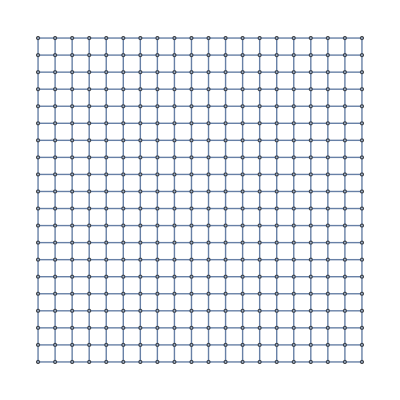

```mathematica
g=GridGraph[{20,20},EdgeWeight->RandomInteger[10,760]]
```

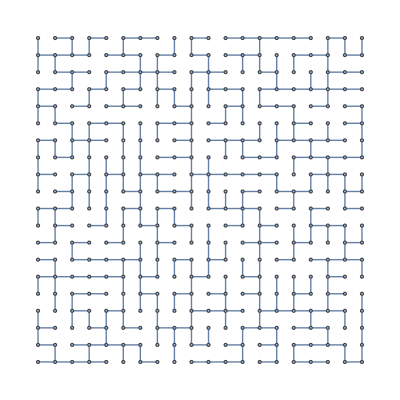

```mathematica
tree=FindSpanningTree[g]
```

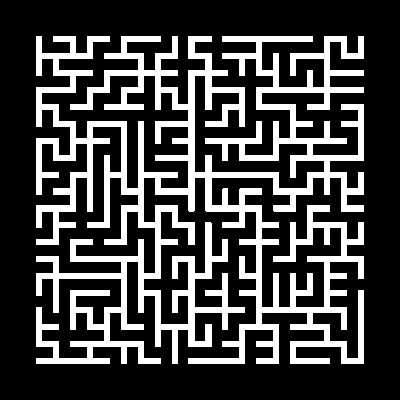

```mathematica
maze=Graph[tree,Background->Black,BaseStyle->{White,Opacity[1],EdgeForm[]},EdgeShapeFunction->(Rectangle[#1[[1]]+0.15,#1[[2]]-0.15]&),VertexShapeFunction->(Rectangle[#1+0.15,#1-0.15]&)]
```

```mathematica
img=Image[maze]
```

-Graphics-

```mathematica
pos[x_,y_]:=Flatten[Table[{i+x,j+y}->White,{i,7},{j,5}]]
img=ReplaceImageValue[img, pos[352,7]~Join~pos[0,346]]
```

-Graphics-

```mathematica
path=Image[WatershedComponents[img],"Bit"]
```

-Graphics-

```mathematica
ImageMultiply[img,path]
```

-Graphics-

```mathematica
ReplaceImageValue[img,#->Red&/@ImageValuePositions[path,Black]]
```

-Graphics-